mu and tau mass at 15 digits accuracy, like a double precision

```mathematica
mumass=0.1`15
taumass=1.7`15
```

0.1

1.7

Expression in LFV process

```mathematica
illog=Log[
(s-mj^2-3mi^2-Sqrt[1-4mi^2/s]Sqrt[(s-mi^2)^2-2mj^2(s+mi^2)+mj^4])/
(s-mj^2-3mi^2+Sqrt[1-4mi^2/s]Sqrt[(s-mi^2)^2-2mj^2(s+mi^2)+mj^4])
]
```

Log[(-3 mi^2-mj^2+s-√(1-(4 mi^2)/s) √(mj^4+(-mi^2+s)^2-2 mj^2 (mi^2+s)))/(-3 mi^2-mj^2+s+√(1-(4 mi^2)/s) √(mj^4+(-mi^2+s)^2-2 mj^2 (mi^2+s)))]

Plot the log as function of Sqrt[s], as one sees it fails already around 300 GeV

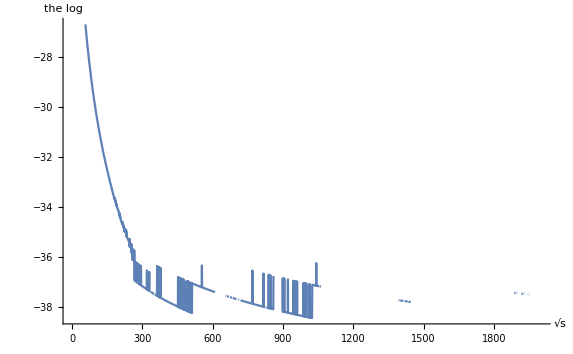

```mathematica
Plot[illog/.{mi->mumass,mj->taumass,s->x^2},{x,1,2000},{AxesLabel->{"√s","the log"}}]
```

Here instead I test the typical collinear log via relations between Energy and longitudinal momentum with muon mass

```mathematica
plmu=Sqrt[Energy^2-mumass^2]
Deltaplmu=Energy-plmu
Deltaplmu/.Energy->100000`15
```

√(-0.01+Energy^2)

Energy-√(-0.01+Energy^2)

5.×10^-8

Problems seems to rather appear in the PeV range, If I put mass of electron the range is the TeV range

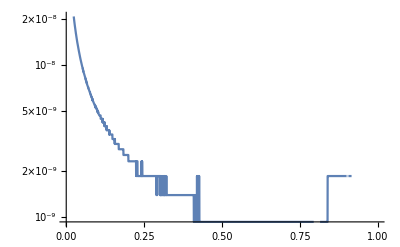

```mathematica
LogPlot[Deltaplmu,{Energy,1,10000000}]
```

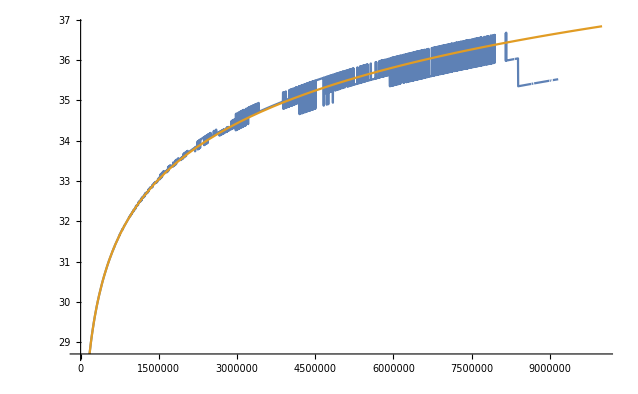

```mathematica
Plot[{Log[(Energy^2)/(Energy^2-plmu^2)],Log[(Energy^2)/mumass^2]},{Energy,1,10000000}]
```

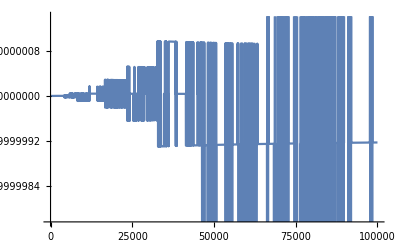

```mathematica
Plot[Log[(Energy^2)/(Energy^2-plmu^2)]/Log[(Energy^2)/mumass^2],{Energy,1,100000}]
```

```mathematica
(Energy^2)/(Energy^2-plmu^2)/.Energy->1000.`15
```

1.×10^8